```mathematica
Simplify[((ⅇ^y+ⅇ^-y)/2 Sin[x])^2+((ⅇ^-y-ⅇ^y)/2 Cos[x])^2]
```

1/4 (ⅇ^(-2 y)+ⅇ^(2 y)-2 Cos[x]^2+2 Sin[x]^2)

```mathematica
Reduce[(ⅇ^(-2x)+ⅇ^(2x))/4-1/2>=0,x,Reals]
```

True

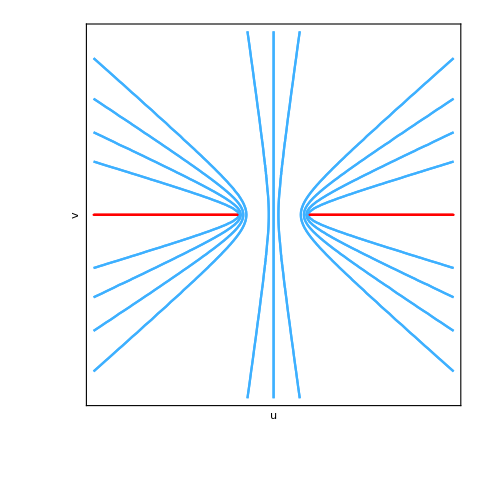

/Users/anirudh/Documents/LaTeX(2)/notes/complex_analysis/figs/chapter_2/sin_map_w.eps

```mathematica
g1=Table[
ContourPlot[
(u/(Sin[a]+10^-10))^2-(v/(Cos[a]+10^-10))^2==1,{u,-5,5},{v,-5,5},
Axes->True,
AxesLabel->{u,v},
FrameTicks->None,
ImageSize->480,
ContourStyle->96],
{a,-5,5,1}];
g2=RegionPlot[x≤-1,{x,-5,-1},{y,-10^-10-10^-10,-10^-10+10^-10},BoundaryStyle->Red];
g3=RegionPlot[x≥1,{x,1,5},{y,-10^-10-10^-10,-10^-10+10^-10},BoundaryStyle->Red];
Show@@{g1,g2,g3}
Export[FileNameJoin[{NotebookDirectory[],"sin_map_w"<>".eps"}],Show@@{g1,g2,g3}]
```

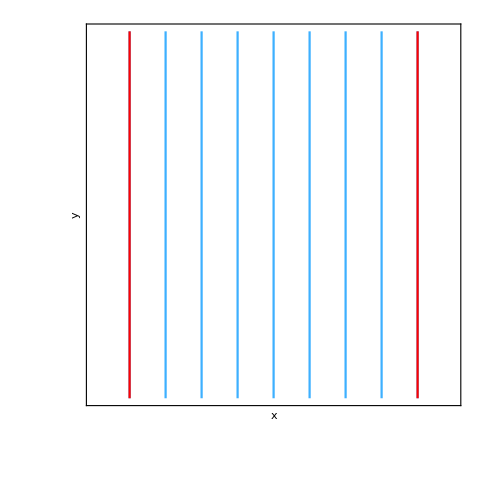

/Users/anirudh/Documents/LaTeX(2)/notes/complex_analysis/figs/chapter_2/sin_map_z.eps

```mathematica
g11=Table[
ContourPlot[
x==a,{x,-5,5},{y,-5,5},
Axes->True,
AxesLabel->{x,y},
FrameTicks->None,
ImageSize->480,
ContourStyle->96],
{a,-5,5,1}];
g12=ContourPlot[
x==4,{x,-5,5},{y,-5,5},
Axes->True,
AxesLabel->{x,y},
FrameTicks->None,
ImageSize->480,
ContourStyle->Red];
g13=ContourPlot[
x==-4,{x,-5,5},{y,-5,5},
Axes->True,
AxesLabel->{x,y},
FrameTicks->None,
ImageSize->480,
ContourStyle->Red];
Show@@{g11,g12,g13}
Export[FileNameJoin[{NotebookDirectory[],"sin_map_z"<>".eps"}],Show@@{g11,g12,g13}]
```

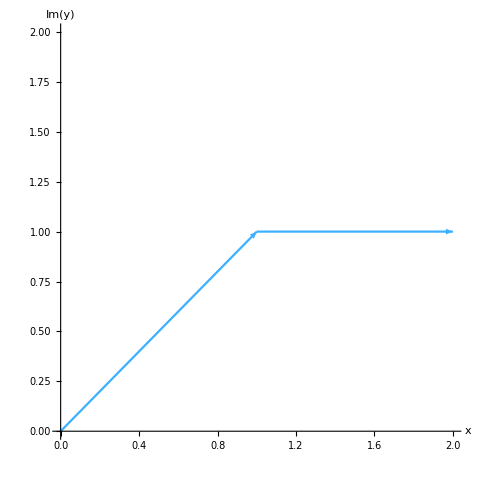

/Users/anirudh/Documents/LaTeX(2)/notes/complex_analysis/figs/chapter_2/curve_ex_1.eps

```mathematica
styles={
Axes->True,
FrameTicks->None,
AxesLabel->{"x","Im(y)"},
ImageSize->480,
PlotRange->{{0,2},{0,2}},
PlotStyle->96
};
g1=ParametricPlot[{t,t},{t,0,1},##]&@@styles;
g2=ParametricPlot[{Piecewise[{{t,1≤t≤2}}], 1},{t,1,2},##]&@@styles;
toExport=Show@@{g1,g2}/.Line[x_]:>{Arrowheads[{0.,0.0,0.0,0.04,0.}],Arrow[x]}
Export[FileNameJoin[{NotebookDirectory[],"curve_ex_1"<>".eps"}],toExport]
```

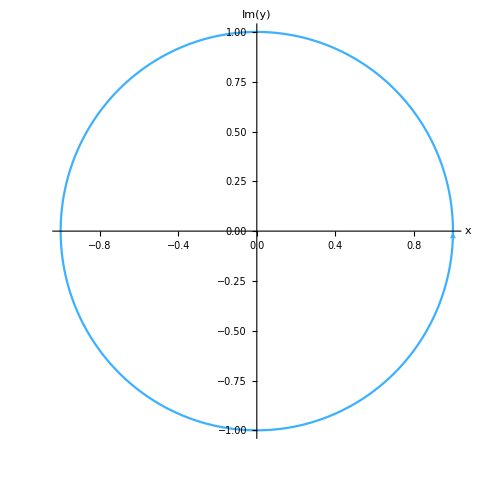

/Users/anirudh/Documents/LaTeX(2)/notes/complex_analysis/figs/chapter_2/curve_ex_2.eps

```mathematica
styles={
Axes->True,
FrameTicks->None,
AxesLabel->{"x","Im(y)"},
ImageSize->480,
PlotStyle->96
};
g3=ParametricPlot[{Cos[t],Sin[t]},{t,0,2π},##]&@@styles;
toExport=g3/.Line[x_]:>{Arrowheads[{0.,0.04,0.02,0.04,0.}],Arrow[x]}
Export[FileNameJoin[{NotebookDirectory[],"curve_ex_2"<>".eps"}],toExport]
```

```mathematica
ParametricPlot[{{2Cos[t],2Sin[t]},{2Cos[t],Sin[t]},{Cos[t],2Sin[t]},{Cos[t],Sin[t]}},{t,0,2Pi},PlotLegends->"Expressions"]
```

```mathematica
Integrate[ⅇ^x Sin@x,{x,0,π}]
```

1/2 (1+ⅇ^π)

```mathematica
styles={
Axes->True,
FrameTicks->None,
AxesLabel->{"x","Im(y)"},
ImageSize->480,
PlotStyle->96
};
g1=ParametricPlot[Callout[{0,t},"C_1",{-0.15,0.48},{-0.01,0.6}],{t,0,1},##]&@@styles;
g2=ParametricPlot[Callout[{t,1},"C_2",{0.5,0.9}],{t,0,1},##]&@@styles;
g3=ParametricPlot[Callout[{t,t},"C_3",{0.5,0.4}],{t,0,1},##]&@@styles;
toExport=Show@@{g1,g2,g3}/.Line[x_]:>{Arrowheads[{0.,0.04,0.0,0.04,0.}],Arrow[x]}
Export[FileNameJoin[{NotebookDirectory[],"ci_contour_ex_1"<>".eps"}],toExport]
```

-Graphics-

/Users/anirudh/Documents/LaTeX(2)/notes/complex_analysis/figs/chapter_2/ci_contour_ex_1.eps